```mathematica
(* Computations for master Equation on a Sphere*)

Integrate[1/2 /Sqrt[1 + 1 - 2 z],{z,-1,1}]
```

1

```mathematica
Integrate[z^2/2 /Sqrt[1 + 1 - 2 z],{z,-1,1}]
```

7/15

```mathematica
SCC =Solve[{9  C1 + 6 C2 ==1,3C1 + 12 C2==7/15},{C1,C2}][[1]]
```

{C1→23/225,C2→1/75}

```mathematica
(*
\left(\De{1 1'}\De{4 4'}-\De{1 4'}\De{4 1'}\right)\left(C_1\De{2 4}\De{2' 4'}+C_2\left(\De{2 2'}\De{4 4'}+ \De{2 4'}\De{4 2'}\right)\right)
*)
SymRule = {De[i_,j_/; j < i] :> De[j,i], De[i_,i_] :> 3};
```

```mathematica
DeltaRule = {De[i_,j_]  De[i_,k_] :> De[j,k],De[i_,j_]  De[k_,j_] :> De[i,k]}
```

{De[i_,j_] De[i_,k_]:>De[j,k],De[i_,j_] De[k_,j_]:>De[i,k]}

```mathematica
EE = ((De[1,5]De[4,8]-De[1,8]De[4,5])
(C1 De[2,4]De[6,8]+C2(De[2,6]De[4,8]+ De[2,8]De[4 ,6]))/.SCC)//Expand
```

-1/75 De[1,8] De[2,8] De[4,5] De[4,6]-1/75 De[1,8] De[2,6] De[4,5] De[4,8]+1/75 De[1,5] De[2,8] De[4,6] De[4,8]+1/75 De[1,5] De[2,6] De[4,8]^2-23/225 De[1,8] De[2,4] De[4,5] De[6,8]+23/225 De[1,5] De[2,4] De[4,8] De[6,8]

```mathematica
(EE/.SymRule)//.DeltaRule
```

-23/225 De[1,6] De[2,4] De[4,5]+23/225 De[1,5] De[2,4] De[4,6]+1/75 De[1,5] De[2,6] De[4,8]^2-1/75 De[1,2] De[5,6]

```mathematica
DeltaRule1 = {De[i_,j_]  De[j_,k_] :> De[i,k]}
```

{De[i_,j_] De[j_,k_]:>De[i,k]}

```mathematica
((EE/.SymRule)//.DeltaRule)//.DeltaRule1
```

-23/225 De[1,6] De[2,5]+23/225 De[1,5] De[2,6]+1/75 De[1,5] De[2,6] De[4,8]^2-1/75 De[1,2] De[5,6]

```mathematica
DeltaRule2 = {De[i_,j_]^2 :> 3}
```

{De[i_,j_]^2:>3}

```mathematica
Res =(((EE/.SymRule)//.DeltaRule)//.DeltaRule1)/.DeltaRule2
```

-23/225 De[1,6] De[2,5]+32/225 De[1,5] De[2,6]-1/75 De[1,2] De[5,6]

```mathematica
WRule1 = W[a_,b_] De[a_,b_]:>0;
WRule2 =  De[a_,b_] De[c_,d_]W[a_,c_] W[b_,d_]:> TWW;
```

```mathematica
A = Expand[2Pi W[1 ,2] W[5,6] Res]/.WRule1
```

-46/225 π De[1,6] De[2,5] W[1,2] W[5,6]+64/225 π De[1,5] De[2,6] W[1,2] W[5,6]

```mathematica
AA = A//.WRule2
```

(64 π TWW)/225-46/225 π De[1,6] De[2,5] W[1,2] W[5,6]

```mathematica
SymWRule = {W[i_,j_/; j < i] :> W[j,i]}
```

{W[i_,j_/;j<i]:>W[j,i]}

```mathematica
WRule3 = {De[a_,b_] W[a_,c_]:> W[b,c]}
```

{De[a_,b_] W[a_,c_]:>W[b,c]}

```mathematica
AAA = AA/.WRule3
```

(64 π TWW)/225-46/225 π De[2,5] W[5,6] W[6,2]

```mathematica
AAAA = AAA/.De[2,5] W[5,6] W[6,2]->TWW
```

(2 π TWW)/25

```mathematica
gamma = (4 Pi/15)/(8 Pi/25)
```

5/6

```mathematica
Integrate[ 1/2z /Sqrt[ 1 + 1 - 2  z],{z,-1,1}]
```

1/3

```mathematica
Integrate[ 1/2z^3 /Sqrt[ 1 + 1 - 2  z],{z,-1,1}]
```

9/35

```mathematica
(*
&&G_1(|\vec r|)\left(3\vec r^2+2\vec r^2\right)+G_2(|\vec r|)\vec r^2=\VEV{\frac{\vec r\cdot\vec r'}{|\vec r- \vec r'|}}_{\vec r'\in S_2}= \ot;\\
    &&G_1(|\vec r|) 3 r^4+G_2(|\vec r|)\vec r^6= \VEV{\frac{(\vec r\cdot\vec r')^3}{|\vec r- \vec r'|}}_{\vec r'\in S_2}= \frac{9}{35}\vec r^2

*)
Solve[{5 G1 + G2 == 1/3, 3 G1 + G2==9/35},{G1, G2}][[1]]
```

{G1→4/105,G2→1/7}

```mathematica
4/105 (-6)
```

-8/35

```mathematica
1/2 + (-8/35)(-5/6)/r^5
```

1/2+4/(21 r^5)

```mathematica
((1/2+4/(21 r^5))/.r->1 )- 5/6
```

-1/7

```mathematica
(* Phi^+ = Wrr/2 +  4/21 Wrr/R^4*)
```

```mathematica
(* Symbolic gradient  G[X_,a_] = \d/X/\d r_a *)
```

```mathematica
G[Wrr,a_] := 2Wr[a];
G[Wr[a_],b_] := W[a,b];
W[a_,a_] := 0;
G[r[a_],b_] := KroneckerDelta[a,b];
G[C_ B_, a_] := G[C,a] B + C G[B,a];
G[C_+ B_, a_] := G[C,a] + G[B,a];
G[ R^n_., a_] :=  n R^(n-2)r[a];
G[C_?NumericQ, a_] :=0;
G[U_,a_,b_] := G[G[U,a],b];
```

```mathematica
SabPos= G[Wrr/2+(4 Wrr)/(21 R^5),a,b]//Expand
```

-(20 Wrr a,b)/(21 R^7)+(20 Wrr r[a] r[b])/(3 R^9)+W[a,b]+(8 W[a,b])/(21 R^5)-(40 r[b] Wr[a])/(21 R^7)-(40 r[a] Wr[b])/(21 R^7)

```mathematica
SabNeg = -1/7 W[a,b]
```

-1/7 W[a,b]

```mathematica
Sab = (((SabPos + SabNeg)/2)/.R->1)//Expand
```

-10/21 Wrr a,b+10/3 Wrr r[a] r[b]+13/21 W[a,b]-20/21 r[b] Wr[a]-20/21 r[a] Wr[b]

```mathematica
-5/252 Wrr a,b+5/36 Wrr r[a] r[b]+29/84 W[a,b]-5/126 r[b] Wr[a]-5/126 r[a] Wr[b]
```

-5/252 Wrr a,b+5/36 Wrr r[a] r[b]+29/84 W[a,b]-5/126 r[b] Wr[a]-5/126 r[a] Wr[b]

```mathematica
Sab/.{ a,b->3,r[a] r[b]->1,W[a,b] ->0,r[b] Wr[a]->Wrr, r[a] Wr[b]->Wrr}
```

0

```mathematica
A =.;
B =.;
```

```mathematica
W0 = DiagonalMatrix[{A,B,-A-B}];
X = {x,y,z};
W0R = W0.X;
```

```mathematica
SubW = {Wrr ->X.W0.X, Wr[n_] :> W0R[[n]], r[n_] :> X[[n]], W[a_,b_] :> W0[[a,b]]}
```

{Wrr→A x^2+B y^2+(-A-B) z^2,Wr[n_]:>W0R⟦n⟧,r[n_]:>X⟦n⟧,W[a_,b_]:>W0⟦a,b⟧}

```mathematica
{Wrr->A x^2+B y^2+(-A-B) z^2,Wr[n_]:>W0R⟦n⟧,r[n_]:>X⟦n⟧,W[a_,b_]:>W0⟦a,b⟧}
```

{Wrr→A x^2+B y^2+(-A-B) z^2,Wr[n_]:>W0R⟦n⟧,r[n_]:>X⟦n⟧,W[a_,b_]:>W0⟦a,b⟧}

```mathematica
Sab
```

-10/21 Wrr a,b+10/3 Wrr r[a] r[b]+13/21 W[a,b]-20/21 r[b] Wr[a]-20/21 r[a] Wr[b]

```mathematica
Strain = Table[Sab/.SubW,{a,1,3},{b,1,3}]//Simplify
```

{{10/21 (B (-1+7 x^2) (y^2-z^2)+A (7 x^4+z^2-x^2 (5+7 z^2))),10/21 x y (A (-2+7 x^2-7 z^2)+B (-2+7 y^2-7 z^2)),10/21 x z (B (2+7 y^2-7 z^2)+7 A (x^2-z^2))},{10/21 x y (A (-2+7 x^2-7 z^2)+B (-2+7 y^2-7 z^2)),10/21 (A (-1+7 y^2) (x^2-z^2)+B (7 y^4+z^2-y^2 (5+7 z^2))),10/21 y z (A (2+7 x^2-7 z^2)+7 B (y^2-z^2))},{10/21 x z (B (2+7 y^2-7 z^2)+7 A (x^2-z^2)),10/21 y z (A (2+7 x^2-7 z^2)+7 B (y^2-z^2)),10/21 (A (5 z^2-7 z^4+x^2 (-1+7 z^2))+B (5 z^2-7 z^4+y^2 (-1+7 z^2)))}}

```mathematica
(Tr[Strain]//Simplify)/.{z^2->1-x^2-y^2}
```

0

```mathematica
DD[x_,y_,z_, A_, B_] = Sqrt[6]Tr[Strain^3]/(Tr[Strain^2])^(3/2)//Simplify
```

(√6 ((A (5 z^2-7 z^4+x^2 (-1+7 z^2))+B (5 z^2-7 z^4+y^2 (-1+7 z^2)))^3+(B (-1+7 x^2) (y^2-z^2)+A (7 x^4+z^2-x^2 (5+7 z^2)))^3+(A (-1+7 y^2) (x^2-z^2)+B (7 y^4+z^2-y^2 (5+7 z^2)))^3))/((A (5 z^2-7 z^4+x^2 (-1+7 z^2))+B (5 z^2-7 z^4+y^2 (-1+7 z^2)))^2+(B (-1+7 x^2) (y^2-z^2)+A (7 x^4+z^2-x^2 (5+7 z^2)))^2+(A (-1+7 y^2) (x^2-z^2)+B (7 y^4+z^2-y^2 (5+7 z^2)))^2)^(3/2)

```mathematica
Plot3D[DD[x,y,Sqrt[1-x^2-y^2],1,1],{x,-1,1},{y,-1,1},RegionFunction->Function[{x,y},x^2+y^2≤1]]
```

-Graphics3D-

```mathematica
F11[x_,y_] = DD[x,y,Sqrt[1-x^2-y^2],1,1]//Factor
```

-((2-21 x^2+21 x^4-3 y^2+21 x^2 y^2) (2-3 x^2-21 y^2+21 x^2 y^2+21 y^4) (4-24 x^2+21 x^4-24 y^2+42 x^2 y^2+21 y^4))/(2 (4-48 x^2+213 x^4-315 x^6+147 x^8-48 y^2+318 x^2 y^2-693 x^4 y^2+441 x^6 y^2+213 y^4-693 x^2 y^4+588 x^4 y^4-315 y^6+441 x^2 y^6+147 y^8)^(3/2))

```mathematica
Plot3D[{F11[x,y]  ,x^2 + y^2 < 1},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Sy =Solve[(2-21 x^2+21 x^4-3 y^2+21 x^2 y^2)==0,y][[2]]
```

{y→(√(-2+21 x^2-21 x^4))/(√3 √(-1+7 x^2))}

```mathematica
Sx =Solve[4-24 x^2+21 x^4-24 y^2+42 x^2 y^2+21 y^4==0,{x}][[4]]
```

{x→(√(12+2 √15-21 y^2))/(√21)}

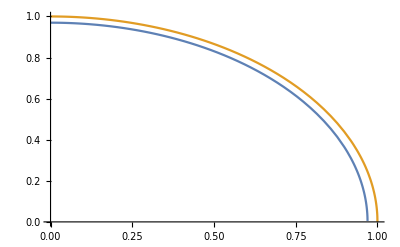

```mathematica
Plot[{x/.Sx,Sqrt[1-y^2]},{y,0,1}]
```

```mathematica
N[Sx/.y->1]
```

{x→0.+0.244368 ⅈ}

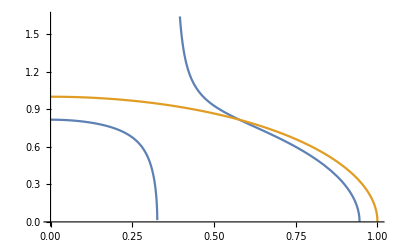

```mathematica
Plot[{y/.Sy,Sqrt[1-x^2]},{x,0,1}]
```